```mathematica
(* SquareDuino - Note Count Computation *)
(* (c) 2014, Alfred "Ben" Roney, Ph.D. *)
(* All rights reserved. *)

(* I think the notes are off by an octave. *)
(* Either adjust the prescaler or fix this notebook. *)
(* Will measure and update soon. *)
```

```mathematica
centsError[ps_,f0_]:=1200FullSimplify[Log[2,f0+1/(16/2^ps 10^6)]-Log[2,f0]]
```

```mathematica
Table[{ps,2^ps,(16 10^6)/2^ps,centsError[ps,4000]},{ps,0,10}]//N//MatrixForm
```

(0. | 1. | 1.6×10^7 | 2.70506×10^-8
1. | 2. | 8.×10^6 | 5.41009×10^-8
2. | 4. | 4.×10^6 | 1.08202×10^-7
3. | 8. | 2.×10^6 | 2.16404×10^-7
4. | 16. | 1.×10^6 | 4.32809×10^-7
5. | 32. | 500000. | 8.65617×10^-7
6. | 64. | 250000. | 1.73123×10^-6
7. | 128. | 125000. | 3.46247×10^-6
8. | 256. | 62500. | 6.92494×10^-6
9. | 512. | 31250. | 0.0000138499
10. | 1024. | 15625. | 0.0000276997)

64

3.8147

-1319.75

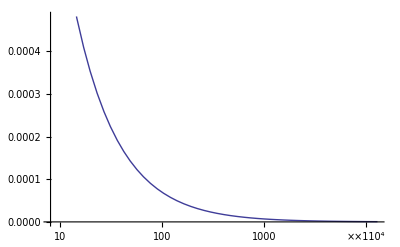

```mathematica
(* using a timer prescaler of 64 results in a clock rate of 500 kHz *)
(* and leaves enough room for a semitone pitch bend *)
psVal :=6
2^psVal
(2^psVal((16 10^6)/2^16)^-1)^-1//N
1200Log[2,%/8.1758]
LogLinearPlot[centsError[psVal,f0],{f0,8,13000}]

psVal = .
```

```mathematica
timerRes[prescale_,clockFreq_,nTimingBits_]:=(prescale(clockFreq)^-1)
timerRes[1024,16 10^6,16]//N
%^-1
```

0.000064

15625.

```mathematica
(* This is a table of frequencies corresponding to midi note values *)
ftab=Table[440/32 2^((i-9)/12),{i,0,127}];
N[ftab]
```

{8.1758,8.66196,9.17702,9.72272,10.3009,10.9134,11.5623,12.2499,12.9783,13.75,14.5676,15.4339,16.3516,17.3239,18.354,19.4454,20.6017,21.8268,23.1247,24.4997,25.9565,27.5,29.1352,30.8677,32.7032,34.6478,36.7081,38.8909,41.2034,43.6535,46.2493,48.9994,51.9131,55.,58.2705,61.7354,65.4064,69.2957,73.4162,77.7817,82.4069,87.3071,92.4986,97.9989,103.826,110.,116.541,123.471,130.813,138.591,146.832,155.563,164.814,174.614,184.997,195.998,207.652,220.,233.082,246.942,261.626,277.183,293.665,311.127,329.628,349.228,369.994,391.995,415.305,440.,466.164,493.883,523.251,554.365,587.33,622.254,659.255,698.456,739.989,783.991,830.609,880.,932.328,987.767,1046.5,1108.73,1174.66,1244.51,1318.51,1396.91,1479.98,1567.98,1661.22,1760.,1864.66,1975.53,2093.,2217.46,2349.32,2489.02,2637.02,2793.83,2959.96,3135.96,3322.44,3520.,3729.31,3951.07,4186.01,4434.92,4698.64,4978.03,5274.04,5587.65,5919.91,6271.93,6644.88,7040.,7458.62,7902.13,8372.02,8869.84,9397.27,9956.06,10548.1,11175.3,11839.8,12543.9}

```mathematica
timerCounts/.Solve[targetTime==timerResolution(timerCounts+1),timerCounts][[1]]
periodToCount[targetTime_,prescale_,clockFreq_,nTimingBits_]=FullSimplify[%/.timerResolution->timerRes[prescale,clockFreq,nTimingBits]]
(*countTab=periodToCount[1/2 1/#,64,16 10^6,16]&/@ftab//N*)
Round[(1/2 1/#-timerRes[64,16 10^6,16])/timerRes[64,16 10^6,16]&/@ftab//N]//InputForm
```

(targetTime-timerResolution)/timerResolution

-1+(clockFreq targetTime)/prescale

{15288, 14430, 13620, 12855, 12134, 11453, 10810, 10203, 9630, 9090, 8580, 8098, 7644, 7214, 6809, 6427, 
 6066, 5726, 5404, 5101, 4815, 4544, 4289, 4049, 3821, 3607, 3404, 3213, 3033, 2862, 2702, 2550, 2407, 
 2272, 2144, 2024, 1910, 1803, 1702, 1606, 1516, 1431, 1350, 1275, 1203, 1135, 1072, 1011, 955, 901, 
 850, 803, 757, 715, 675, 637, 601, 567, 535, 505, 477, 450, 425, 401, 378, 357, 337, 318, 300, 283, 
 267, 252, 238, 224, 212, 200, 189, 178, 168, 158, 149, 141, 133, 126, 118, 112, 105, 99, 94, 88, 83, 
 79, 74, 70, 66, 62, 59, 55, 52, 49, 46, 44, 41, 39, 37, 35, 33, 31, 29, 27, 26, 24, 23, 21, 20, 19, 18, 
 17, 16, 15, 14, 13, 12, 12, 11, 10, 10, 9}

```mathematica
ftab[[70]]
```

440